# Лабораторная работа №4

## Численное решение нелинейных уравнений

Михалькевич Д.Н.
гр. 221701

Вариант 8

## Задание 1.

### Отделите графически корни алгебраического уравнения f (x) = 0 с помощью функции Plot. Найдите один из них (нецелый) с точностью ξ = 10^-3 методом хорд. Укажите потребовавшееся число итераций. Проиллюстрируйте графически нахождение первых двух приближений (постройте график функции и хорды).

```mathematica
f[x_]:=12 x^3+29 x^2-52x+11;
ϵ = 10^-3;
a = 0.7;
b = -0.5;
```

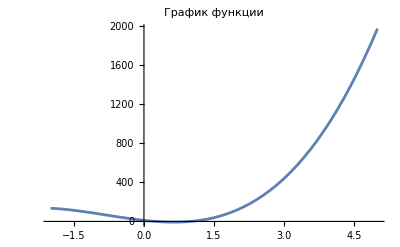

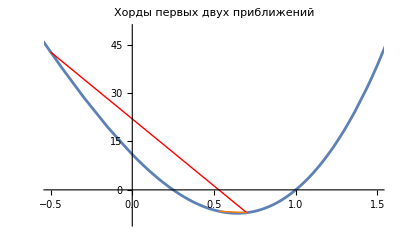

Найденный корень: 0.249974; Число итераций: 6

```mathematica
initialPlot = Plot[f[x], {x, -2,5}, PlotLabel -> "График функции"];
ChordMethod[f_,a_,b_,eps_]:=Module[{x0=a,x1=b,x2,n=0},While[Abs[f[x1]]>eps&&Abs[x1-x0]>eps,x2=x1-f[x1] (x1-x0)/(f[x1]-f[x0]);
x0=x1;x1=x2;n++;];
{x1,n}];

{root,iterations}=ChordMethod[f,a,b,ϵ];

firstApproximation=Line[{{a,f[a]},{b,f[b]}}];
secondApproximationX=b-f[b] (b-a)/(f[b]-f[a]);
secondApproximation=Line[{{a,f[a]},{secondApproximationX,f[secondApproximationX]}}];
Show[initialPlot]
Show[initialPlot,Graphics[{Red,firstApproximation, Orange,secondApproximation}],PlotRange->{{-0.5,1.5},{-10,50}},PlotLabel->"Хорды первых двух приближений"]

Print["Найденный корень: ", N[root, 4], "; Число итераций: ", iterations];
```

## Задание 2.

#### Отделите графически и найдите с помощью функций Solve, NSolve, Roots, FindRoot корни алгебраического уравнения f (x) = 0. Разложите многочлен f (x) на множители,используя функцию Factor.

```mathematica
Clear[f];
```

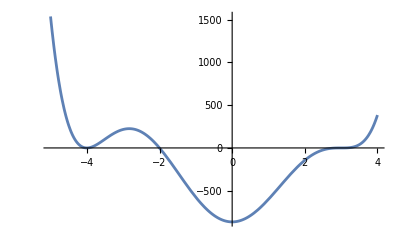

Корни Solve: {{x→-4.},{x→-4.},{x→-2.},{x→3.},{x→3.},{x→3.}}

Корни NSolve: {{x→-4.},{x→-4.},{x→-2.},{x→3.},{x→3.},{x→3.}}

Корни Roots: x==-4.||x==-4.||x==-2.||x==3.||x==3.||x==3.

Корень FindRoot: {x→-4.}

Разложение: (-3+x)^3 (2+x) (4+x)^2

```mathematica
f:=x^6+x^5-31 x^4-13 x^3+306 x^2-864;
Plot[f,{x,-5,4}]
Print["Корни Solve: ", N[Solve[f == 0, x], 1]]
Print["Корни NSolve: ", N[NSolve[f == 0, x], 1]]
Print["Корни Roots: ", N[Roots[f == 0,x], 1]]
Print["Корень FindRoot: ", N[FindRoot[f == 0, {x,-5}], 1]]
Print["Разложение: ", Factor[f]]
```

## Задание 3.

### Отделите графически корни трансцендентного уравнения с помощью функции Plot. Найдите один из них с точностью ξ=10^-3: а) методом Ньютона; б) методом секущих. Укажите потребовавшееся число итераций.

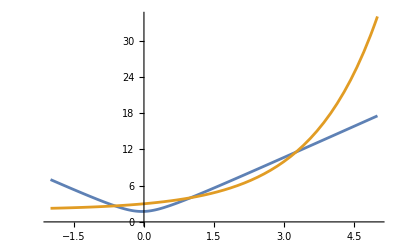

```mathematica
Clear[f];
f[x_] :=√(12 x^2+x+3);
g[x_]:=2^x+2
func[x_]:=√(12 x^2+x+3)-2^x-2
initialPlot = Plot[{f[x],g[x]}, {x,-2,5}];
Show[initialPlot]
```

#### Метод Ньютона

```mathematica
NewtF[f_, g_,func_, a_, b_, eps_] :=
	Module[{ NewtonMethod},
NewtonMethod[x0_] :=
			Module[{root, iter = 0},
			root = x0;
			While[Abs[func[root]] > eps && iter < 100,
				root = root-func[root]/func'[root];
				iter++;
			];
			Print[Plot[func[x],{x,a,b}]];	
			Print["Корень = ", root];
			Print["Количество итераций = ", iter];
		];
Print["Метод Ньютона:"];
		NewtonMethod[a];
];
```

Метод Ньютона:

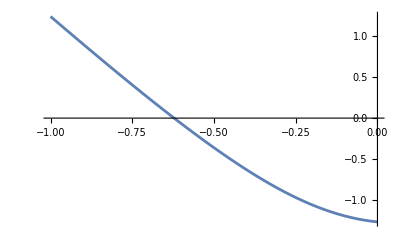

Корень = -0.622097

Количество итераций = 2

Метод Ньютона:

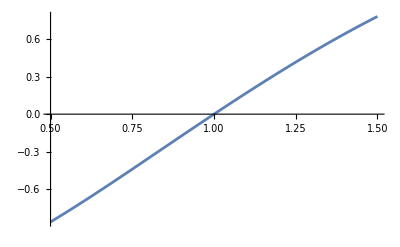

Корень = 0.999645

Количество итераций = 2

Метод Ньютона:

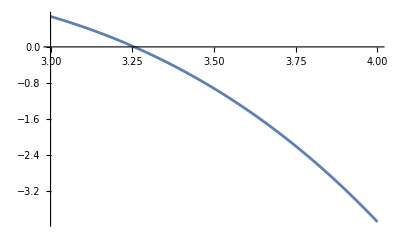

Корень = 3.25594

Количество итераций = 3

```mathematica
NewtF[f, g, func, -1.0,0.0 , 10^(-3)]
NewtF[f, g, func, 0.5,1.5 , 10^(-3)]
NewtF[f, g, func, 3.0,4.0 , 10^(-3)]
```

#### Метод Секущих

```mathematica
SecF[f_, g_,func_, a_, b_, eps_] :=
	Module[{SecantMethod},
		SecantMethod[X0_, X1_] :=
			Module[{x0, x1, root, iter = 1},
			x0 = X0;x1 = X1;
			root = x1 - func[x1] * (x1 - x0) / (func[x1] - func[x0]);
			While[Abs[func[root]] > eps && iter < 100,
				x0 = x1;
				x1 = root;
				root = x1 - func[x1] * (x1 - x0) / (func[x1] - func[x0]);
				iter++;
			];
			Print[Plot[func[x], {x, a, b}]];				
			Print["Корень = ", root];
			Print["Количество итераций = ", iter];
		];
		Print["Метод секущих:"];
		SecantMethod[a, b];
		
	];
SecF[f, g, func, -1.0,0.0 , 10^(-3)]
SecF[f, g, func, 0.5,1.5 , 10^(-3)]
SecF[f, g, func, 3.0,4.0 , 10^(-3)]
```

Метод секущих:

-Graphics-

Корень = -0.621999

Количество итераций = 4

Метод секущих:

-Graphics-

Корень = 1.00001

Количество итераций = 3

Метод секущих:

-Graphics-

Корень = 3.25583

Количество итераций = 4

## Задание 4.

#### Приведите уравнение к виду,пригодному для итераций. Найдите его корни методом простых итераций с точностью ξ=10^-3. Укажите потребовавшееся число итераций.

```mathematica
ClearAll
func[x_] = -12 x^2-3+(2^x+2)^2;
```

ClearAll

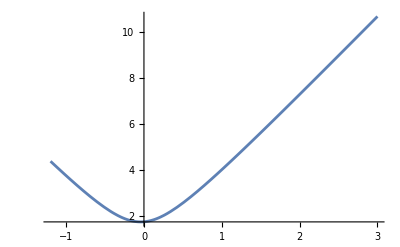

Метод простых итераций:

Корень= 1.08857×10^54

Корень= 2.64442×10^54

```mathematica
F4[func_, a_, b_, eps_] :=
	Module[{SimpleIterMethod},
		Print[Plot[func[x], {x, a, b}]];
			
		SimpleIterMethod[x0_] :=
			Module[{root, iter = 0},
				root = x0;
				While[Abs[func[root]] > eps && iter < 100,
					root = func[root];
					iter++
					];
				Print["Корень= ", root];
			];
		Print["Метод простых итераций:"];
		SimpleIterMethod[-1.1];
		SimpleIterMethod[2.8];
	];
F4[f, -1.2, 3.0, 10^(-3)];
```

## Задание 5.

#### Решите уравнение с помощью функций Solve, NSolve, FindRoot.

```mathematica
solveRoots = Solve[f[x] == 0, x];
nSolveRoots = NSolve[f[x] == 0, x];
findRootRoots = FindRoot[f[x] == 0, {x,0}];

Print["Уравнение решается только с помощью функции FindRoot: ", N[findRootRoots, 4]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Уравнение решается только с помощью функции FindRoot: {x→-0.041668}

### Задание 6

```mathematica
ClearAll;
f[x_, y_] = Sinh[2y-x]-3x+1-y;
g[x_,y_] = (x^2+y^2)^2-32(y^2-x^2);

graph1 = ContourPlot[f[x,y] == 0, {x, -10,10}, {y,-7,15},Axes->True,Frame->False];
graph2 = ContourPlot[g[x,y] == 0, {x, -10,10}, {y,-7,15},Axes->True,Frame->False,ColorFunction->Hue];
Show[graph1, graph2]

FindRoot[{f[x,y] == 0, g[x,y] == 0}, {x,-2}, {y,-3}]
FindRoot[{f[x,y] == 0, g[x,y] == 0}, {x,0}, {y,0}]
FindRoot[{f[x,y] == 0, g[x,y] == 0}, {x,0.5}, {y,0.5}]
FindRoot[{f[x,y] == 0, g[x,y] == 0}, {x,2}, {y,2}]
```

-Graphics-

{x→-1.76022,y→-2.30332}

{x→0.193271,y→-0.193723}

{x→0.336354,y→0.338757}

{x→1.66188,y→2.08239}